```mathematica
Here we calculated the asymptotic expansion for the small thermal lengthscale δ, and produce the Figure 2 from the TVE paper.
```

```mathematica
ClearAll [ "Global`*"]
```

```mathematica
(*Note that some of the material properties below can be calculated from the other specified material properties*)

(* the material properties of RUBBER 2 in TVE FRAMEWORK PAPER*)
subRubberN2 ={"ρ"-> 2300,"K"-> 10^9,"μ"->3.0 10^8,"μ∞"-> 2.0 10^7,"τ"-> 1.0 10^-6,"γ"->1.0088 ,"κ"->2.0, "Cv"-> 1288.58,"T0"-> 300,"α"-> 2.5 10^-4};

(*The properties of air*)
subAirN ={"μ"->0,"λ"->100721,"κ"->0.026, "ημ"-> 1.85*10^-5,"ηλ"->-1.253333 10^-6, "ηK"-> 1.108*10^-5,"ρ"->1.19,"Cv"-> 722.86,"T0"-> 300,"α"-> 1/300.0,"K"-> 100.721*10^3,"γ"->1.3902992};

(*The properties of water*)
subWaterN ={"μ"->0,"λ"->2.14*^9,"κ"->0.58, "ημ"-> 8.9 10^-4,"ηλ"->0.00023, "ηK"-> 2.47/3 10^-3,"ρ"-> 998,"Cv"-> 4.182 10^3,"T0"-> 300,"α"-> 2.57 10^-4,"K"-> 2.14 10^9, "Cp"->4224.4884,"γ"->1.0101598361716257};

(*Substitute the non-dimensionals for material properties*)
subString= { 
δ -> kϕ^2/kθ^2 ,
kθ^2-> ⅈ("Cv")/("κ")"ρ" ω,kθ^n_:>  ( ⅈ("Cv")/("κ")"ρ" ω)^(n/2),
kϕ^2-> ("ρ" ω^2)/("βω" + 4/3 "μω"),kϕ^n_:>  (("ρ" ω^2)/("βω" + 4/3 "μω"))^(n/2),
Lϕ-> ⅈ pT ω/("κ" "T0"),
Lθ-> -   (pT/("βω" + 4/3 "μω")),
 "T0"-> "ρ" ("Cv")/(("α")^2"K")("γ"-1)
}/.pT-> "α" "K" "T0";
subKV = {"μω" -> "μ" -ⅈ ω "ημ","λω" -> "λ" -ⅈ ω"ηλ","βω" -> "K" -ⅈ ω"ηK"};

subSLM = {"μω" -> "μ∞" -("μ" - "μ∞") (ⅈ ω "τ")/(1- ⅈ ω "τ"),"λω" -> "K" -2/3"μω" ,"βω" -> "K"};


(*The only assumptions we need to use is that kϕ^2== kθ^2 δ = O(δ) and Lθ Lϕ ~ kθ^2 = O(1)  *)
(*
Choosing the branchcut:
because kθ^2-Lθ Lϕ ~ a ⅈ - b, where a,b >0 and b<<a, then √((kθ^2-Lθ Lϕ)^2)== √((a ⅈ - b)^2)== - a ⅈ + b == -kθ^2+Lθ Lϕ  
*)
subroot1={ √((kθ^2-Lθ Lϕ)^2)-> -kθ^2+Lθ Lϕ ,1/√((kθ^2-Lθ Lϕ)^2)->1/(-kθ^2+Lθ Lϕ )} ;
subroot2={ √((kθ^2-Lθ Lϕ)^2)-> kθ^2-Lθ Lϕ ,1/√((kθ^2-Lθ Lϕ)^2)->1/(kθ^2-Lθ Lϕ )} ;
a =1/2(kθ^2+kϕ^2-Lθ Lϕ); b= √(a^2-kθ^2 kϕ^2);
term = a+b;

(*For liquids*)
expand1[term_,n_]:=Normal@ Simplify[Simplify[Series[term//.{kϕ^2-> kθ^2 δ},{δ,0,n}]//.subroot1]/.subroot1];

(*Without assuming*)
expand[term_,n_]:=Normal[Series[term//.{kϕ^2-> kθ^2 δ},{δ,0,n}]]

(*Double checking Mathematica branch for sqrt*)
θ = -Pi/2 + 0.1;
Sqrt[(ⅇ^(ⅈ θ))^2]- ⅇ^(ⅈ θ);
ComplexPlot[Sqrt[(z)^2]- z,{z,-1-I,1+I}];

θ =- Pi + 0.1;
ComplexPlot[Sqrt[(z)^2]+ z,{z,-1-I,1+I}];
```

```mathematica
(*Choose your material*)
modelLabels = {"Air","Water","Rubber 2"};
subNs={subAirN,subWaterN,subRubberN2};
subModels={subKV,subKV,subSLM};
subModelNs =( subString~Join~subModels[[#]]~Join~subNs[[#]])&/@Range@Length@subNs;


(*Range of values used for the frequency*)
ωsolid = 0.1/"τ"/.subRubberN2;
ωglassy = 5.0/"τ"/.subRubberN2;
ωmin = Min[ωsolid,2Pi 10^5]
ωmax = Max[ωglassy,2Pi 10^7]
ωs = Range[ωmin,ωmax,(ωmax-ωmin)/30.0];
```

100000.

20000000 π

```mathematica
(*A list of the relative error commited for kp, when, in order, using an expansion up to O(δ), O(δ^2), ...*)
maxn = 3; (*largest δ expansion order*)

(*Used to calculate the error over frequency*)
errorFunction=Norm;
errorFunction=Max;

kpErrors[subModel_] :=Table[
θ =  Arg[kθ^2-Lθ Lϕ//.subModel/.ω-> Mean[ωs]];
kp = If[Abs[θ ]< π/2 ,a-b,a+b] //.subModel;
kpN = expand1[a+b,n]//.subModel;

errorFunction[(Abs[(kpN - kp)/kp]/.ω-> #)&/@ωs]
,{n,1,maxn}];

(*A list of the relative error commited for kp, when, in order, using an expansion up to O(δ), O(δ^2), ...*)
kTErrors[subModel_] :=Table[ 
θ =  Arg[kθ^2-Lθ Lϕ//.subModel/.ω-> Mean[ωs]];
kT =If[Abs[θ]< π/2, a+b,a-b]//.subModel ;
kTN = expand1[a-b,n]//.subModel;
errorFunction[(Abs[(kTN - kT)/kT]/.ω-> #)&/@ωs]
,{n,0,maxn-1}];

kpserror=kpErrors/@subModelNs
ktserror=kTErrors/@subModelNs
```

{{0.00452993,0.0000320652,1.39798×10^-8},{1.32213×10^-7,1.31713×10^-7,1.31713×10^-7},{4.3244×10^-7,4.61172×10^-9,4.61172×10^-9}}

{{0.00452946,0.0000525727,3.72138×10^-7},{4.05431×10^-8,1.6038×10^-13,1.86576×10^-15},{4.32447×10^-7,2.97494×10^-11,2.08246×10^-15}}

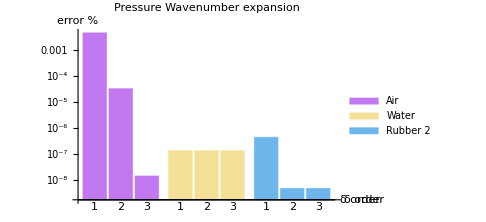

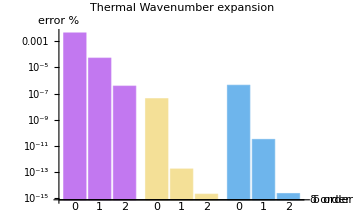

```mathematica
SetOptions[BarChart,BaseStyle->FontSize->17];

bar=BarChart[kpserror,ScalingFunctions->"Log",
ImageSize->Medium,
PlotLabel->"Pressure Wavenumber expansion",
ChartLegends->{modelLabels,None},
ChartLabels-> Range@maxn,
AxesLabel->{"δ order","error %"},
ChartStyle->{"Pastel",None}]

(*
Export[NotebookDirectory[]<>"pressure-wavenumber-expansion-δ="<>ToString[maxn]<>"-"<>ToString[errorFunction]<>".pdf",bar]
Export[NotebookDirectory[]<>"pressure-wavenumber-expansion.pdf",bar]
*)
bar= BarChart[ktserror,ScalingFunctions->"Log",
ImageSize->Medium,
PlotLabel->"Thermal Wavenumber expansion",
ChartLabels-> Range@maxn -1,
AxesLabel->{"δ order","error %"},
ChartStyle->{"Pastel",None}]

(*
Export[NotebookDirectory[]<>"thermal-wavenumber-expansion"<>ToString[maxn]<>"-"<>ToString[errorFunction]<>".pdf",bar]
Export[NotebookDirectory[]<>"thermal-wavenumber-expansion.pdf",bar]
*)
```

## Approximating the wavevectors

```mathematica
(*Below this section is a discussion on how to write the wavevectors. Below I am just going to calculate the error made by using the exact wavevector in the paper but with approximate wavenumbers.*)

(*below k is the wavenumber which could be thermal or pressure dominated*)
V = (k^2-kϕ^2)/Lθ/.subString;

maxn = 3; (*largest δ expansion order*)

(*Used to calculate the error over frequency*)
errorFunction=Norm;
errorFunction=Max;
ClearAll[VpErrors]


VpErrors[subModel_] :=Table[
θ =  Arg[kθ^2-Lθ Lϕ//.subModel/.ω-> Mean[ωs]];
kp2 = If[Abs[θ ]< π/2 ,a-b,a+b] //.subModel;
kpN2 = expand1[a+b,n]//.subModel;
Vp =V//.subModel/.k^2->kp2;
VpN =V//.subModel/.k^2->kpN2;

errorFunction[(Abs[Vp-VpN]/Abs[Vp]/.ω-> #)&/@ωs]
,{n,1,maxn}];

VTErrors[subModel_] :=Table[
θ =  Arg[kθ^2-Lθ Lϕ//.subModel/.ω-> Mean[ωs]];
kT2 =If[Abs[θ]< π/2, a+b,a-b]//.subModel ;
kTN2 = expand1[a-b,n]//.subModel;
Vt =V//.subModel/.k^2->kT2;
VtN =V//.subModel/.k^2->kTN2;

errorFunction[(Abs[Vt-VtN]/Abs[Vt]/.ω-> #)&/@ωs]
,{n,1,maxn}];

subModel = subModelNs[[1]];
VpErrors/@subModelNs
VTErrors/@subModelNs
```

{{0.0116068,0.0000821594,3.58199×10^-8},{0.0000132002,0.0000131938,0.0000131938},{0.0000687933,5.1203×10^-7,5.1203×10^-7}}

{{0.0000525833,3.72213×10^-7,1.62277×10^-10},{1.60538×10^-13,1.8413×10^-15,1.84129×10^-15},{2.97496×10^-11,2.06327×10^-15,9.23029×10^-16}}

### Errors for the asymptotic form of the wavevectors

```mathematica
V = (k^2-kϕ^2)/Lθ;

errorFunction=Max;

VpδErrors[subModel_] :=Table[
θ =  Arg[kθ^2-Lθ Lϕ//.subModel/.ω-> Mean[ωs]];
kp2 = If[Abs[θ ]< π/2 ,a-b,a+b] //.subModel;
(*kpNs = expand1[a+b,n]//.subModel;*)
Vp = V/.k^2->kp2//.subModel;
Vpδ =expand1[V/.{k^2-> a+b},n]//.subModel;

errorFunction[(Abs[(Vp - Vpδ)/Vp]/.ω-> #)&/@ωs]
,{n,1,maxn}];

VTδErrors[subModel_] :=Table[ 
θ =  Arg[kθ^2-Lθ Lϕ//.subModel/.ω-> Mean[ωs]];
kT2 =If[Abs[θ]< π/2, a+b,a-b]//.subModel ;
(*kTNs = expand1[a-b,n]//.subModel;*)
VT = V/.k^2->kT2//.subModel;
VTδ =expand1[V/.{k^2-> a-b},n]//.subModel;

errorFunction[(Abs[(VT - VTδ)/VT]/.ω-> #)&/@ωs]
,{n,1,maxn}];

Vpδs=VpδErrors/@subModelNs
VTδs=VTδErrors/@subModelNs
```

{{0.0116068,0.0000821594,3.58199×10^-8},{0.0000132002,0.0000131938,0.0000131938},{0.0000687933,5.1203×10^-7,5.1203×10^-7}}

{{0.0000525833,3.72213×10^-7,1.62277×10^-10},{1.60201×10^-13,1.95628×10^-15,1.95628×10^-15},{2.97494×10^-11,2.09106×10^-15,1.10753×10^-15}}

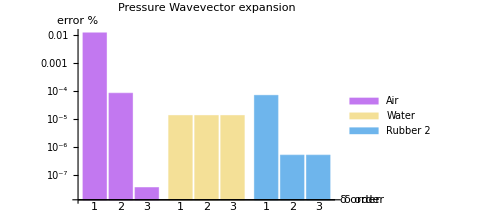

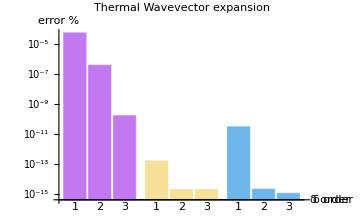

```mathematica
SetOptions[BarChart,BaseStyle->FontSize->17];

bar=BarChart[Vpδs,ScalingFunctions->"Log",
ImageSize->Medium,
PlotLabel->"Pressure Wavevector expansion",
ChartLegends->{modelLabels,None},
ChartLabels-> Range@maxn,
AxesLabel->{"δ order","error %"},
ChartStyle->{"Pastel",None}]

(*Export[NotebookDirectory[]<>"pressure-wavenumber-expansion-δ="<>ToString[maxn]<>"-"<>ToString[errorFunction]<>".pdf",bar]*)
(*Export[NotebookDirectory[]<>"pressure-wavevector-expansion.pdf",bar]*)

bar= BarChart[VTδs,ScalingFunctions->"Log",
ImageSize->Medium,
PlotLabel->"Thermal Wavevector expansion",
ChartLabels-> Range@maxn,
AxesLabel->{"δ order","error %"},
ChartStyle->{"Pastel",None}]

(*Export[NotebookDirectory[]<>"thermal-wavevector-expansion.pdf",bar]*)
```